```mathematica
Clear["Global`*"]
```

# Continuous quantum correction on Markovian and non - Markovian models

By Juan Garcia Nila and Todd A Brun

## One qubit with continuous quantum error correction

Uusing equation (23), we obtain the single - qubit Markovian fidelity with continuous bit flip errors and correction, as a function of time $\gamma t$ for different values of the ratio $r = \frac {\eta} {\gamma} $

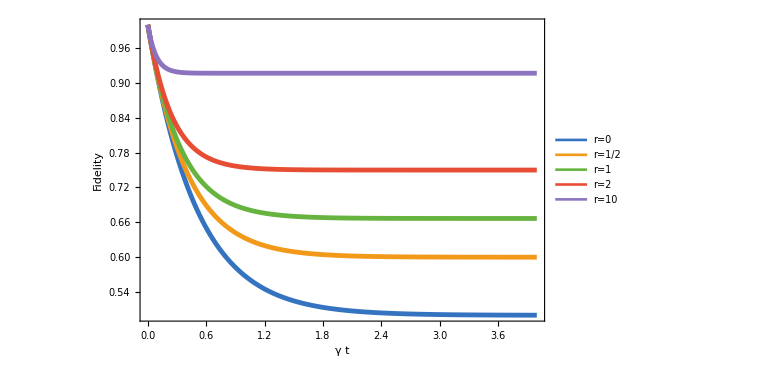

/Users/jgarcian/Documents/Paper2026/Images/markovfidel2.pdf

```mathematica
Clear["Global`*"]
figAM1Model[t_,r_]:=(1+r)/(2+r)+1/(2+r) Exp[-(2+r) t];

(*----------parameters----------*)
figAM1RList={0,1/2,1,2,10};
figAM1TGrid=N@Range[0,4,0.01];

(*----------numeric datasets----------*)
figAM1DataSets=Table[Transpose[{figAM1TGrid,figAM1Model[#,r]&/@figAM1TGrid}],{r,figAM1RList}];

(*----------long-format export data----------*)
figAM1LongData=Flatten[MapIndexed[Function[{dataset,idx},With[{r=N@figAM1RList[[idx[[1]]]]},({r,#[[1]],#[[2]]}&/@dataset)]],figAM1DataSets],1];

Export["/Users/jgarcian/Documents/Paper2026/Datasets/markovfidel2_long.csv",Prepend[figAM1LongData,{"r","t","Fidelity"}],"CSV"];

(*----------styles----------*)
figAM1Styles={Directive[Thickness[0.006],RGBColor[0.20,0.45,0.75]],Directive[Thickness[0.006],RGBColor[0.95,0.60,0.10]],Directive[Thickness[0.006],RGBColor[0.40,0.70,0.25]],Directive[Thickness[0.006],RGBColor[0.90,0.30,0.20]],Directive[Thickness[0.006],RGBColor[0.55,0.45,0.75]]};

(*----------plot from numeric data----------*)
figAM1Plot=ListLinePlot[figAM1DataSets,PlotStyle->figAM1Styles,InterpolationOrder->3,PlotRange->{{0,4},{0.5,1}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Automatic},FrameLabel->{{Style["Fidelity",25],None},{Style[Row[{γ," t"}],25],None}},LabelStyle->Directive[Black,23],PlotLegends->Placed[LineLegend[(Row[{"r=",#}]&/@figAM1RList),LegendMarkerSize->23],Right],AspectRatio->0.66,ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/markovfidel2.pdf",figAM1Plot]
```

### Non - Markovian system bath X - X coupling with a cooling bath (Shengshi Pang)

```mathematica
Clear["Global`*"]
M[α_,κ_]:={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-κ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-κ/2,0,0,0,0,-2α,0,0,0,0,0,0,0,0},{κ,0,0,-κ,0,0,2α,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-κ/2,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2α,0,0,-κ/2,0,0,0,0,0,0,0,0,0},{0,0,2α,0,κ,0,0,-κ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-2α,0,0},{0,0,0,0,0,0,0,0,0,-κ/2,0,0,-2α,0,0,0},{0,0,0,0,0,0,0,0,0,0,-κ/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,κ,0,0,-κ,0,0,0,0},{0,0,0,0,0,0,0,0,0,2α,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2α,0,0,0,0,-κ/2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-κ/2,0},{0,0,0,0,0,0,0,0,0,0,0,0,κ,0,0,-κ}}
M[α,κ]//MatrixForm
v0[x0_,y0_,z0_]:={1/4,0,0,1/4,x0/4,0,0,x0/4,y0/4,0,0,y0/4,z0/4,0,0,z0/4}
MatrixForm[v0[x0,y0,z0]];
vf=MatrixExp[M[α,κ]].v0[x0,y0,z0];
FullSimplify[{vf[[1]],vf[[5]],vf[[9]],vf[[13]]}]
A[α_,κ_,η_]:={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-κ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-κ/2,0,0,0,0,-2α,0,0,0,0,0,0,0,0},{κ,0,0,-κ,0,0,2α,0,0,0,0,0,0,0,0,0},{0,0,0,0,-η,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-κ/2-η,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2α,0,0,-κ/2-η,0,0,0,0,0,0,0,0,0},{0,0,2α,0,κ,0,0,-κ-η,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-η,0,0,0,0,-2α,0,0},{0,0,0,0,0,0,0,0,0,-κ/2-η,0,0,-2α,0,0,0},{0,0,0,0,0,0,0,0,0,0,-κ/2-η,0,0,0,0,0},{0,0,0,0,0,0,0,0,κ,0,0,-κ-η,0,0,0,0},{η,0,0,0,0,0,0,0,0,2α,0,0,-η,0,0,0},{0,η,0,0,0,0,0,0,2α,0,0,0,0,-κ/2-η,0,0},{0,0,η,0,0,0,0,0,0,0,0,0,0,0,-κ/2-η,0},{0,0,0,η,0,0,0,0,0,0,0,0,κ,0,0,-κ-η}}
MatrixForm[A[α,κ,η]]

vfcorr=MatrixExp[A[α,κ,η]].v0[x0,y0,z0];
(*FullSimplify[{vfcorr[[1]],vfcorr[[5]],vfcorr[[9]],vfcorr[[13]]}]*)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | -2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
κ | 0 | 0 | -κ | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 α | 0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 α | 0 | κ | 0 | 0 | -κ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ/2 | 0 | 0 | -2 α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | 0 | 0 | -κ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | -κ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | 0 | 0 | -κ)

{1/4,x0/4,1/4 ⅇ^(-κ/4) y0 (Cosh[1/4 √(-64 α^2+κ^2)]+(κ Sinh[1/4 √(-64 α^2+κ^2)])/(√(-64 α^2+κ^2))),1/4 ⅇ^(-κ/4) z0 (Cosh[1/4 √(-64 α^2+κ^2)]+(κ Sinh[1/4 √(-64 α^2+κ^2)])/(√(-64 α^2+κ^2)))}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | -2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
κ | 0 | 0 | -κ | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 α | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 α | 0 | κ | 0 | 0 | -η-κ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | 0 | -2 α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | -2 α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | 0 | 0 | -η-κ | 0 | 0 | 0 | 0
η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | -η | 0 | 0 | 0
0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0
0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0
0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | 0 | 0 | -η-κ)

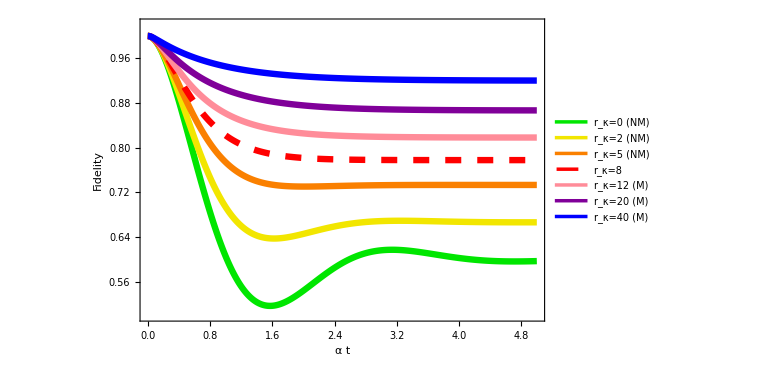

/Users/jgarcian/Documents/Paper2026/Images/fidkappa.pdf

```mathematica
figKappaFidEta=1;   (*eta=gamma in the x-axis label gamma t*)
figKappaFidAlpha=1;   (*choose alpha=1 to match the shown threshold kappa=8*)
figKappaFidKList={0,2,5,8,12,20,40};

figKappaFidTMin=0;figKappaFidTMax=5;figKappaFidDt=0.01;
figKappaFidTGrid=N@Range[figKappaFidTMin,figKappaFidTMax,figKappaFidDt];

(*----------Eq.(11):C(t)----------*)
figKappaFidC[t_,κ_,α_,η_]:=Piecewise[{{Exp[-(η+κ/4) t]*((κ/Sqrt[64 α^2-κ^2]) Sin[(t/4) Sqrt[64 α^2-κ^2]]+Cos[(t/4) Sqrt[64 α^2-κ^2]]),κ^2<64 α^2},{Exp[-(η+κ/4) t]*((κ/Sqrt[κ^2-64 α^2]) Sinh[(t/4) Sqrt[κ^2-64 α^2]]+Cosh[(t/4) Sqrt[κ^2-64 α^2]]),κ^2>64 α^2},{Exp[-(η+2 α) t] (1+2 α t),κ^2==64 α^2}}];

(*----------Eq.(12):D(t)----------*)
figKappaFidD[t_,κ_,α_,η_]:=Piecewise[{{(η (κ+2 η))/(η (κ+2 η)+8 α^2)*(1+Exp[-(η+κ/4) t]*(((32 α^2)/(κ+2 η)-κ)*(Sin[(t/4) Sqrt[64 α^2-κ^2]]/Sqrt[64 α^2-κ^2])-Cos[(t/4) Sqrt[64 α^2-κ^2]])),κ^2<64 α^2},{(η (κ+2 η))/(η (κ+2 η)+8 α^2)*(1+Exp[-(η+κ/4) t]*(((32 α^2)/(κ+2 η)-κ)*(Sinh[(t/4) Sqrt[κ^2-64 α^2]]/Sqrt[κ^2-64 α^2])-Cosh[(t/4) Sqrt[κ^2-64 α^2]])),κ^2>64 α^2},{(η (η+4 α))/((η+2 α)^2)*(1+Exp[-(η+2 α) t]*(((4 α^2)/(4 α+η)-2 α) t-1)),κ^2==64 α^2}}];

(*----------Fidelity used in the plot----------*)
figKappaFidF[t_,κ_]:=(1+figKappaFidC[t,κ,figKappaFidAlpha,figKappaFidEta]+figKappaFidD[t,κ,figKappaFidAlpha,figKappaFidEta])/2

(*----------Build NUMERIC datasets:{gamma t,Fidelity}----------*)
figKappaFidDataSets=Table[Transpose[{figKappaFidTGrid,figKappaFidF[#,κ]&/@figKappaFidTGrid}],{κ,figKappaFidKList}];

(*----------Export numeric data in long format (MapIndexed)----------*)
figKappaFidLongData=Flatten[MapIndexed[Function[{dataset,idx},With[{κ=N@figKappaFidKList[[idx[[1]]]]},({κ,#[[1]],#[[2]]}&/@dataset)]],figKappaFidDataSets],1];

Export["/Users/jgarcian/Documents/Paper2026/Datasets/fidkappa_datasets_long.csv",Prepend[figKappaFidLongData,{"kappa","alpha_t","Fidelity"}],"CSV"];

(*----------Styles (color+dashed boundary at kappa=8)----------*)
figKappaFidStyles={Directive[Thickness[0.008],RGBColor[0.0,0.9,0.0]],(*k=0 green*)Directive[Thickness[0.008],RGBColor[0.95,0.90,0.0]],(*k=2 yellow*)Directive[Thickness[0.008],RGBColor[0.98,0.50,0.0]],(*k=5 orange*)Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0],Dashing[{0.02,0.02}]],(*k=8 dashed red*)Directive[Thickness[0.008],RGBColor[1.0,0.55,0.60]],(*k=12 pink*)Directive[Thickness[0.008],RGBColor[0.5,0.0,0.6]],(*k=20 purple*)Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]]       (*k=40 blue*)};

figKappaFidLegendLabels=Table[With[{κ=figKappaFidKList[[i]]},Which[κ<8,Row[{Subscript[r,"κ"],"=",κ," (NM)"}],κ==8,Row[{Subscript[r,"κ"],"=",κ}],κ>8,Row[{Subscript[r,"κ"],"=",κ," (M)"}]]],{i,Length[figKappaFidKList]}];

(*----------Plot (NUMERIC ONLY)----------*)
figKappaFidPlot=ListLinePlot[figKappaFidDataSets,PlotStyle->figKappaFidStyles,InterpolationOrder->3,PlotRange->{{0,5},{0.5,1.02}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Automatic},FrameLabel->{{Style["Fidelity",25],None},{Style[Row[{α," t"}],25],None}},LabelStyle->Directive[Black,23],PlotLegends->Placed[LineLegend[figKappaFidLegendLabels,LegendMarkerSize->23],Right],AspectRatio->0.66,ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/fidkappa.pdf",figKappaFidPlot]
```

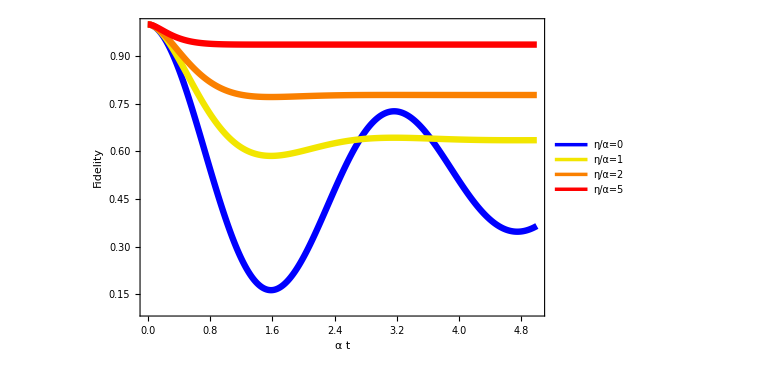

/Users/jgarcian/Documents/Paper2026/Images/fidRkappa1NEW.pdf

```mathematica
etaKappa=1;                 
etaAlpha=1;
etaRatios={0,1,2,5};     (*η/α values*)

tGrid=N@Range[0,5,0.01];

(*C(t):only two cases (no boundary)*)
etaC[t_?NumericQ,κ_?NumericQ,α_?NumericQ,η_?NumericQ]:=If[κ^2<64 α^2,Module[{Δ=Sqrt[64 α^2-κ^2]},N@(Exp[-(η+κ/4) t]*((κ/Δ) Sin[(t/4) Δ]+Cos[(t/4) Δ]))],Module[{Δ=Sqrt[κ^2-64 α^2]},N@(Exp[-(η+κ/4) t]*((κ/Δ) Sinh[(t/4) Δ]+Cosh[(t/4) Δ]))]];

(*D(t):only two cases (no boundary)*)
etaD[t_?NumericQ,κ_?NumericQ,α_?NumericQ,η_?NumericQ]:=If[κ^2<64 α^2,Module[{Δ=Sqrt[64 α^2-κ^2],pref},pref=(η (κ+2 η))/(η (κ+2 η)+8 α^2);
N@(pref*(1+Exp[-(η+κ/4) t]*(((32 α^2)/(κ+2 η)-κ)*(Sin[(t/4) Δ]/Δ)-Cos[(t/4) Δ])))],Module[{Δ=Sqrt[κ^2-64 α^2],pref},pref=(η (κ+2 η))/(η (κ+2 η)+8 α^2);
N@(pref*(1+Exp[-(η+κ/4) t]*(((32 α^2)/(κ+2 η)-κ)*(Sinh[(t/4) Δ]/Δ)-Cosh[(t/4) Δ])))]];
(*Fidelity*)
etaF[t_?NumericQ,κ_?NumericQ,α_?NumericQ,η_?NumericQ]:=N@((1+etaC[t,κ,α,η]+etaD[t,κ,α,η])/2);

(*numeric datasets*)
dataSets=Table[With[{η=ratio*etaAlpha},Transpose[{tGrid,etaF[#,etaKappa,etaAlpha,η]&/@tGrid}]],{ratio,etaRatios}];

(*export long-format CSV (MapIndexed pattern)*)
longData=Flatten[MapIndexed[Function[{dataset,idx},With[{ratio=N@etaRatios[[idx[[1]]]]},({ratio,#[[1]],#[[2]]}&/@dataset)]],dataSets],1];

(*fidRkappa1NEW*)
Export["/Users/jgarcian/Documents/Paper2026/Datasets/fidRkappa1NEW_etaSweep_numeric_datasets_long.csv",Prepend[longData,{"eta_over_alpha","t","Fidelity"}],"CSV"];

(*styles*)
styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],Directive[Thickness[0.008],RGBColor[0.95,0.90,0.0]],Directive[Thickness[0.008],RGBColor[0.98,0.50,0.0]],Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]};

(*plot from numeric data*)
fidRkappa1NEWPlot=ListLinePlot[dataSets,InterpolationOrder->3,PlotStyle->styles,PlotRange->{{0,5},{0.1,1.0}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Automatic},FrameLabel->{{Style["Fidelity",25],None},{Style["α t",25],None}},LabelStyle->Directive[Black,23],PlotLegends->Placed[LineLegend[(Row[{η,"/",α,"=",#}]&/@etaRatios),LegendMarkerSize->23],Right],AspectRatio->0.65,ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/fidRkappa1NEW.pdf",fidRkappa1NEWPlot]
```

## Post - Markovian Master Equation (PMME)

### Exponential kernel

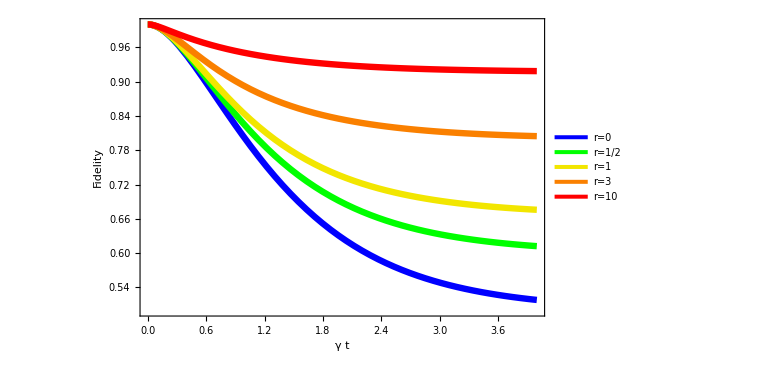

/Users/jgarcian/Documents/Paper2026/Images/correcta.pdf

```mathematica
ClearAll["Global`*"];
ktilde[u_,a_,c_]:=a/(u+c);

(*----ξ(t)----*)
ξTilde[s_,a_,c_,γ_,η_]:=1/(s+η+2 γ ktilde[s+2 γ+η,a,c]);

ξInvLap[t_,a_,c_,γ_?NumericQ,η_?NumericQ]:=Assuming[{a>0,c>0,γ>0,η>=0,t>=0},FullSimplify@InverseLaplaceTransform[ξTilde[s,a,c,γ,η],s,t]];
ξFun[t_,a_,c_,γ_,η_]:=Module[{D1},D1=Sqrt[(c/2+γ)^2-2 γ a];
Exp[-(c/2+γ+η) t]*(((c/2+γ)/D1) Sinh[t D1]+Cosh[t D1])];

(*----χ(t)----*)
ChiTilde[s_,a_,c_,γ_,η_]:=(η/(2 s)-(γ η/(2 γ+η)) (ktilde[s,a,c]-ktilde[s+2 γ+η,a,c])/s)/(s+η+2 γ ktilde[s+2 γ+η,a,c]);

χInvLap[t_,a_?NumericQ,c_?NumericQ,γ_?NumericQ,η_?NumericQ]:=Assuming[t>=0&&a>0&&c>0&&γ>0&&η>=0,FullSimplify[InverseLaplaceTransform[ChiTilde[s,a,c,γ,η],s,t]]];

χFun[t_,a_,c_,γ_,η_]:=Module[{D2,D1,denom1,denom2,denom3},D2=Sqrt[(c+2 γ)^2-8 a γ];
D1=Sqrt[(c/2+γ)^2-2 γ a];
denom1=2 γ a+η (c+2 γ+η);
denom2=2 a γ+η (c+2 γ+η);
denom3=-2 γ a+(c-η) (2 γ+η);
(η/2)*(c+2 γ+η)/denom1+(η/2)*Exp[-(c/2+γ+η) t]*(((4 a γ-(c+2 γ) (c+2 γ+η))/denom2)*(Sinh[(t/2) D2]/D2)-((c+2 γ+η)/denom2)*Cosh[(t/2) D2])+(a γ η)/denom3*(Exp[-c t]-Exp[-(c/2+γ+η) t]*(Cosh[t D1]-(Sinh[t D1]/(2 D1))*(c-2 (γ+η))))];

FidelityInv[t_,a_,c_,γ_,η_]:=(1+ξInvLap[t,a,c,γ,η]+2 χInvLap[t,a,c,γ,η])/2

(*======================*)
tGrid=Subdivide[0.1,3,50];
etaRatios={0,1,10};
(*numeric datasets*)
dataSets=Table[With[{η=ratio},Transpose[{tGrid,FidelityInv[#,1,1,1,η]&/@tGrid}]],{ratio,etaRatios}];
(*export long-format CSV (MapIndexed pattern)*)
longData=Flatten[MapIndexed[Function[{dataset,idx},With[{ratio=N@etaRatios[[idx[[1]]]]},({ratio,#[[1]],#[[2]]}&/@dataset)]],dataSets],1];
(*correcta*)
Export["/Users/jgarcian/Documents/Paper2026/Datasets/correcta_PMME_etaSweep_datasets_long.csv",Prepend[longData,{"eta_over_gamma","t","Fidelity"}],"CSV"];


styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],Directive[Thickness[0.008],RGBColor[0.0,1.0,0.0]],Directive[Thickness[0.008],RGBColor[0.95,0.90,0.0]],Directive[Thickness[0.008],RGBColor[0.98,0.50,0.0]],Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]};

fidPMMEPlot=Plot[{FidelityInv[t,1,1,1,0],FidelityInv[t,1,1,1,0.5],FidelityInv[t,1,1,1,1],FidelityInv[t,1,1,1,3],FidelityInv[t,1,1,1,10]},{t,0,4},PlotStyle->Take[styles],PlotRange->{{0,4},{0.5,1.0}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Automatic},FrameLabel->{{Style["Fidelity",25],None},{Style["γ t",25],None}},LabelStyle->Directive[Black,23],PlotLegends->Placed[{"r=0","r=1/2","r=1","r=3","r=10"},Right],PlotRange->All,AspectRatio->0.65,ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/correcta.pdf",fidPMMEPlot]
```

### Decaying oscillating damped exponential kernel

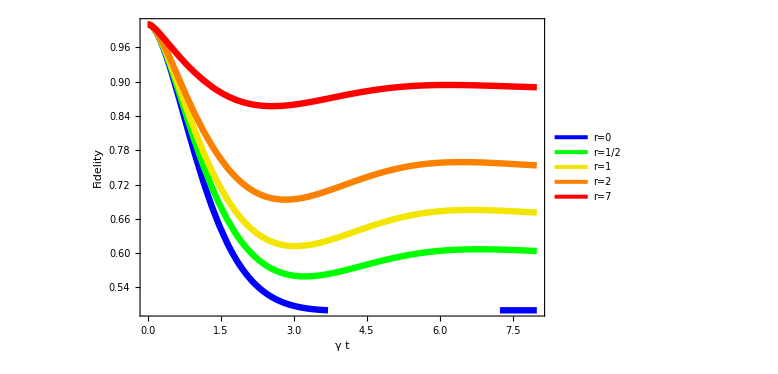

/Users/jgarcian/Documents/Paper2026/Images/plotk2.pdf

```mathematica
ClearAll["Global`*"];
ktilde[s_,a_,c_]:=(s+a)/(s^2+s+c);

(*----ξ----*)
ξTilde[s_,a_,c_,γ_,η_]:=1/(s+η+2 γ ktilde[s+2 γ+η,a,c]);

ξInvLap[t_,a_,c_,γ_?NumericQ,η_?NumericQ]:=Assuming[{a>0,c>0,γ>0,η>=0,t>=0},FullSimplify@InverseLaplaceTransform[ξTilde[s,a,c,γ,η],s,t]];
(*----χ----*)
ChiTilde[s_,a_,c_,γ_,η_]:=(η/(2 s)-(γ η/(2 γ+η)) (ktilde[s,a,c]-ktilde[s+2 γ+η,a,c])/s)/(s+η+2 γ ktilde[s+2 γ+η,a,c]);
χInvLap[t_,a_?NumericQ,c_?NumericQ,γ_?NumericQ,η_?NumericQ]:=Assuming[t>=0&&a>0&&c>0&&γ>0&&η>=0,FullSimplify[InverseLaplaceTransform[ChiTilde[s,a,c,γ,η],s,t]]];

FidelityInv[t_,a_,c_,γ_,η_]:=(1+ξInvLap[t,a,c,γ,η]+2 χInvLap[t,a,c,γ,η])/2

(*======================*)
tGrid=Subdivide[0.1,3,50];
etaRatios={0,1,10};
(*numeric datasets*)
dataSets=Table[With[{η=ratio},Transpose[{tGrid,FidelityInv[#,1,1,1,η]&/@tGrid}]],{ratio,etaRatios}];
(*export long-format CSV (MapIndexed pattern)*)
longData=Flatten[MapIndexed[Function[{dataset,idx},With[{ratio=N@etaRatios[[idx[[1]]]]},({ratio,#[[1]],#[[2]]}&/@dataset)]],dataSets],1];
(*plotk2*)
Export["/Users/jgarcian/Documents/Paper2026/Datasets/plotk2_PMME_etaSweep_datasets_long.csv",Prepend[longData,{"eta_over_gamma","t","Fidelity"}],"CSV"];
(*===============*)

styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],Directive[Thickness[0.008],RGBColor[0.0,1.0,0.0]],Directive[Thickness[0.008],RGBColor[0.95,0.90,0.0]],Directive[Thickness[0.008],RGBColor[0.98,0.50,0.0]],Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]};

fidPMMEOscillPlot=Plot[{(1+ξInvLap[t,1,1,1,0])/2,FidelityInv[t,1,1,1,0.5],FidelityInv[t,1,1,1,1],FidelityInv[t,1,1,1,2],FidelityInv[t,1,1,1,7]},{t,0,8},PlotStyle->Take[styles],PlotRange->{{0,8},{0.5,1.0}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Automatic},FrameLabel->{{Style["Fidelity",20],None},{Style["γ t",20],None}},LabelStyle->Directive[Black,18],PlotLegends->Placed[{"r=0","r=1/2","r=1","r=2","r=7"},Right],PlotRange->All,AspectRatio->0.65,ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/plotk2.pdf",fidPMMEOscillPlot]
```

## The three qubit code

#### Theory

Theory
The LO is the error correction generator and L1 is the lindblad errors of 3 qubit

```mathematica
L0[η_]:=η{{0,1,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
L1[γ_]:=γ{{-3,1,0,0},{3,-3,2,0},{0,2,-3,3},{0,0,1,-3}};
Mat=L0[η]+ L1[γ];
Eigenvalues[Mat]
Eigensystem[Mat]
```

{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))}

{{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))},{{1,(3 γ)/(γ+η),(3 γ)/(γ+η),1},{1,-1,-1,1},{-1,-(-2 γ-η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),-(2 γ+η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),1},{-1,-(-2 γ-η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),-(2 γ+η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),1}}}

Check that the Matrix is obtained by Q Lambda Inv (Q)

```mathematica
Λ=DiagonalMatrix[Eigensystem[Mat][[1]]];
Q=Transpose[Eigensystem[Mat][[2]]];
FullSimplify[Q.Λ.Inverse[Q]]//MatrixForm
Q//MatrixForm
FullSimplify[L1[γ].Q]//MatrixForm;
Λ t//MatrixForm;
MatrixExp[Λ t]//MatrixForm;
FullSimplify[MatrixExp[Λ t].Inverse[Q]]//MatrixForm;
DΛ=DiagonalMatrix[{k0,k1,k2,k3}];
FullSimplify[DΛ.Inverse[Q]]//MatrixForm;
FullSimplify[L1[γ].Q].FullSimplify[DΛ.Inverse[Q]]//MatrixForm;
PmmeMat3=-s IdentityMatrix[4]+L0[η]+FullSimplify[L1[γ].Q].FullSimplify[DΛ.Inverse[Q]];
Func3Qub[s_,γ_,η_,k0_,k1_,k2_,k3_]:=({{-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))), 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))), 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2))))}})
```

(-3 γ | γ+η | 0 | 0
3 γ | -3 γ-η | 2 γ | 0
0 | 2 γ | -3 γ-η | 3 γ
0 | 0 | γ+η | -3 γ)

(1 | 1 | -1 | -1
(3 γ)/(γ+η) | -1 | -(-2 γ-η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)) | -(-2 γ-η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η))
(3 γ)/(γ+η) | -1 | -(2 γ+η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)) | -(2 γ+η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η))
1 | 1 | 1 | 1)

Now let' s define the exponential kernel k (t) = c Exp[-ct] laplace transform

```mathematica
kLap[s_,c_]:=c/(s+c)
Simplify[Inverse[Func3Qub[s,γ,η,kLap[s-Eigensystem[Mat][[1,1]],c],kLap[s-Eigensystem[Mat][[1,2]],c],kLap[s-Eigensystem[Mat][[1,3]],c],kLap[s-Eigensystem[Mat][[1,4]],c]]][[1,1]]]
q0t[t_,γ_,η_,c_]:=InverseLaplaceTransform[Inverse[-Func3Qub[s, γ, η, kLap[s - Eigensystem[Mat][[1, 1]], c], kLap[s - Eigensystem[Mat][[1, 2]], c], kLap[s - Eigensystem[Mat][[1, 3]], c], kLap[s - Eigensystem[Mat][[1, 4]], c]]][[1, 1]], s, t]
q1t[t_,γ_,η_,c_]:=InverseLaplaceTransform[Inverse[-Func3Qub[s, γ, η, kLap[s - Eigensystem[Mat][[1, 1]], c], kLap[s - Eigensystem[Mat][[1, 2]], c], kLap[s - Eigensystem[Mat][[1, 3]], c], kLap[s - Eigensystem[Mat][[1, 4]], c]]][[2, 1]], s, t]
FullSimplify[q0t[t,γ,η,c]]
q0tExplicit[t_,γ_,η_,c_]:=1/-4 (-(6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))-(2 (γ+η))/(4 γ+η)-(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c γ-16 γ^2+c η-13 γ η-η^2-c √(16 γ^2+16 γ η+η^2)-c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)+5 γ √(16 γ^2+16 γ η+η^2)+5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)+η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))
q1tExplicit[t_,γ_,η_,c_]:=3/4 γ (2/(4 γ+η)-(2 c ⅇ^(-t (4 γ+η)))/((c-4 γ-η) (4 γ+η))-(4 ⅇ^(-c t) (c^2+6 γ^2-c (6 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c (-1+ⅇ^(t √(16 γ^2+16 γ η+η^2)))+8 γ+η-√(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (8 γ+η+√(16 γ^2+16 γ η+η^2))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))
```

-(1+(c (s^3+6 γ^2 (γ+η)+s^2 (9 γ+2 η)+s (20 γ^2+9 γ η+η^2)))/(s (s^3+12 γ^2 (4 γ+η)+2 s^2 (6 γ+η)+s (44 γ^2+12 γ η+η^2))))/(c+s)

1/4 ((6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))+(2 (γ+η))/(4 γ+η)+(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (-2 c γ+16 γ^2-c η+13 γ η+η^2+c √(16 γ^2+16 γ η+η^2)+c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)-5 γ √(16 γ^2+16 γ η+η^2)-5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)-η √(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
M3[γ_,η_]:={{-3 γ,η+γ,0,0},{3 γ,-(η+3 γ),2 γ,0},{0,2 γ,-(η+3 γ),3 γ},{0,0,η+γ,-3 γ}}

MatrixForm[M3[γ,η]]
FullSimplify[MatrixExp[M3[γ,η]]]//MatrixForm

FullSimplify[MatrixForm[Dot[MatrixExp[M3[γ,η]],{1,0,0,0}]]]

FullSimplify[((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[1]]]

FullSimplify[((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[1]]+((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[2]]]
```

(-3 γ | γ+η | 0 | 0
3 γ | -3 γ-η | 2 γ | 0
0 | 2 γ | -3 γ-η | 3 γ
0 | 0 | γ+η | -3 γ)

((3 ⅇ^(-4 γ-η) γ)/(8 γ+2 η)+(γ+η)/(8 γ+2 η)+(ⅇ^(-4 γ-η/2-1/2 √(16 γ^2+16 γ η+η^2)) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(ⅇ^(1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (-ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)+ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | 1/2 (γ+η) (1/(4 γ+η)+(ⅇ^(-4 γ-η) ((6 γ)/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))))/(2 (γ+η)))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)+(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]+((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)-(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)-(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]+((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)+(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
1/2 (γ+η) (1/(4 γ+η)+(ⅇ^(-4 γ-η) ((6 γ)/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))))/(2 (γ+η))) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (-ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)+ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | (3 ⅇ^(-4 γ-η) γ)/(8 γ+2 η)+(γ+η)/(8 γ+2 η)+(ⅇ^(-4 γ-η/2-1/2 √(16 γ^2+16 γ η+η^2)) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(ⅇ^(1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)))

((3 ⅇ^(-4 γ-η) γ)/(8 γ+2 η)+(γ+η)/(8 γ+2 η)+(ⅇ^(-4 γ-η/2-1/2 √(16 γ^2+16 γ η+η^2)) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(ⅇ^(1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)+(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)-(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
1/2 (γ+η) (1/(4 γ+η)+(ⅇ^(-4 γ-η) ((6 γ)/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))))/(2 (γ+η))))

1-1/2 t γ (6-3 t (4 γ+η)+t^2 (18 γ^2+10 γ η+η^2))

1+t^2 γ^2 (-3+t (8 γ+η))

For the PMME

```mathematica
kLapExpKernel[s_,c_,λ_]:=c/((s-λ)+c)
L0[η_]:=η{{0,1,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
L1[γ_]:=γ{{-3,1,0,0},{3,-3,2,0},{0,2,-3,3},{0,0,1,-3}};
(*==L0[η]+L1[γ]*)FullSimplify[Transpose[Eigenvectors[L0[η]+L1[γ]]].DiagonalMatrix[Eigenvalues[L0[η]+L1[γ]]].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]]];
(*L1[γ].Q]==*)
FullSimplify[L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]];
(*DΛ.Inverse[Q]*)
DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]];
FullSimplify[(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])]//MatrixForm
PmmeMat3[s_,γ_,η_,k0_,k1_,k2_,k3_]:=-s IdentityMatrix[4]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
PmmeMat3ExpKernel[s_,γ_,η_,c_]:=-s IdentityMatrix[4]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[4]]]}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
q0tNum[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat3ExpKernel[s,γ,η,c]]][[1, 1]],s,t]
overlap3q[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat3ExpKernel[s,γ,η,c]].{1,0,0,0})[[1]],s,t]+ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat3ExpKernel[s,γ,η,c]].{1,0,0,0})[[2]],s,t]
```

(3/4 γ (-(2 (4 k1 γ+k0 η))/(4 γ+η)+k3 (-1-η/(√(16 γ^2+16 γ η+η^2)))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)+k3 (4 γ+η))/(4 γ+η)+(-k3 (8 γ+7 η)+k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)-5 k3 (4 γ+η))/(4 γ+η)+(k3 (16 γ+11 η)-k2 (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)-5 k3 (4 γ+η))/(4 γ+η)+(k3 (16 γ+11 η)-k2 (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)+k3 (4 γ+η))/(4 γ+η)+(-k3 (8 γ+7 η)+k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-(2 (4 k1 γ+k0 η))/(4 γ+η)+k3 (-1-η/(√(16 γ^2+16 γ η+η^2)))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

SetDelayed::write: Tag List in {«1»}[s_,γ_,η_,k0_,k1_,k2_,k3_] is Protected.

$Failed

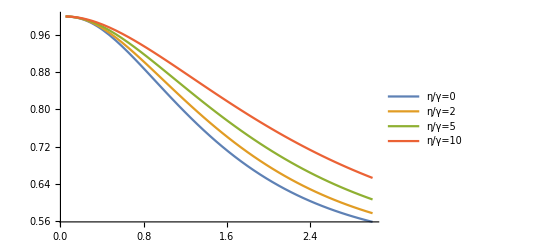

```mathematica
Plot[{overlap3q[t,1,0,1],overlap3q[t,1,2,1],overlap3q[t,1,5,1],overlap3q[t,1,10,1]},{t,0.05,3},PlotLegends->{"η/γ=0","η/γ=2","η/γ=5","η/γ=10"}]
```

### Plot Markov VA PMME for three qubits

For the Markov plot

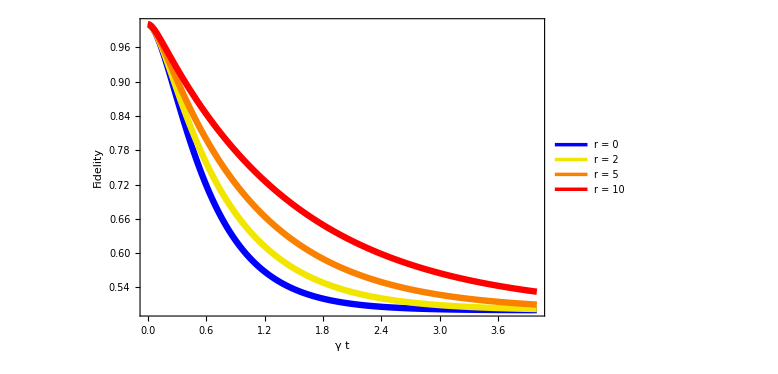

/Users/jgarcian/Documents/Paper2026/Images/3qmarkov.pdf

```mathematica
Clear["Global`*"]
M3[γ_,η_]:={{-3 γ,η+γ,0,0},{3 γ,-(η+3 γ),2 γ,0},{0,2 γ,-(η+3 γ),3 γ},{0,0,η+γ,-3 γ}}
FullSimplify[Dot[MatrixExp[M3[γ,η]t],{1,0,0,0}][[1]]+Dot[MatrixExp[M3[γ,η]t],{1,0,0,0}][[2]]];
Foverlap3[t_,γ_,η_]:=1/(4 √(16 γ^2+16 γ η+η^2))ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (8 (-1+ⅇ^(t √(16 γ^2+16 γ η+η^2))) γ+(-1+ⅇ^(t √(16 γ^2+16 γ η+η^2))) η+(1+ⅇ^(t √(16 γ^2+16 γ η+η^2))+2 ⅇ^(1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2)))) √(16 γ^2+16 γ η+η^2))
etaRatios={0,2,5,10};

tMax=4;
nPts=400;
tGrid=Subdivide[0,tMax,nPts];
dataSets=Table[With[{η=ratio},Transpose@{N@tGrid,N@Foverlap3[#,1,η]&/@tGrid}],{ratio,etaRatios}];

(*long format:{eta_over_alpha,t,Fidelity}*)longData=Flatten[MapIndexed[Function[{dataset,idx},With[{ratio=N@etaRatios[[idx[[1]]]]},({ratio,#[[1]],#[[2]]}&/@dataset)]],dataSets],1];

(*3qmarkov*)
Export["/Users/jgarcian/Documents/Paper2026/Datasets/3qmarkov_etaSweep_numeric_datasets_long.csv",Prepend[longData,{"eta_over_alpha","t","Fidelity"}],"CSV"];

styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],Directive[Thickness[0.008],RGBColor[0.95,0.90,0.0]],Directive[Thickness[0.008],RGBColor[0.98,0.50,0.0]],Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]};

fid3qmarkov=ListLinePlot[dataSets,InterpolationOrder->3,PlotStyle->Take[styles,Length@etaRatios],PlotRange->{{0,tMax},{0.5,1.0}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Automatic},FrameLabel->{{Style["Fidelity",25],None},{Style["γ t",25],None}},LabelStyle->Directive[Black,23],PlotLegends->Placed[LineLegend[(Row[{"r = ",#}]&/@etaRatios),LegendMarkerSize->23],Right],AspectRatio->0.65,ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/3qmarkov.pdf",fid3qmarkov]
```

The Non Markovian PMME plot is

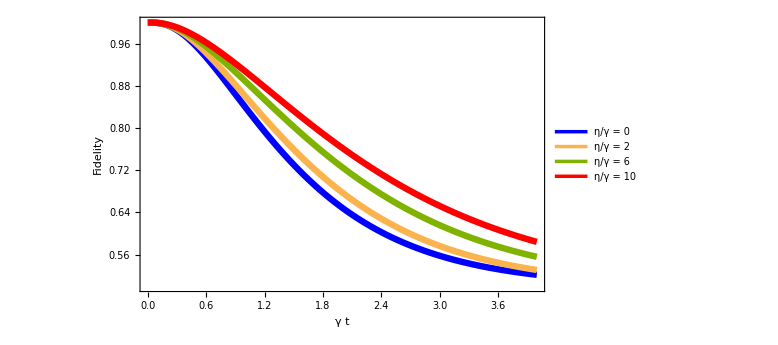

/Users/jgarcian/Documents/Paper2026/Images/pmme3qerror.pdf

```mathematica
Clear["Global`*"]
(* ================PMME Fidelity F(t)====================*)
Fpmme[t_?NumericQ,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=Module[{Δ,denom},Δ=Sqrt[16 γ^2+16 γ η+η^2];
denom=1-(8 γ+η)/c+12 (γ/c)^2;
1/2+(1/2)*(1/denom)*(12 (γ/c)^2 Exp[-c t]+Exp[-t (4 γ+η/2)]*((1-(8 γ+η)/c) Cosh[(t/2) Δ]+(8 γ (1-5 γ/c)+η (1-16 γ/c)-η^2/c)*(Sinh[(t/2) Δ]/Δ)))];
(* =====================*)
(*Parameters for plot*)
(* =====================*)
γval=1.0;          
tMin=0.0;
tMax=4.0;
ηVals={0,2,6,10};
nPts=100;
tGrid=Subdivide[tMin,tMax,nPts];
dataSets=Table[Transpose@{N@tGrid,N@Map[Fpmme[#,γval,η,1]&,tGrid]},{η,ηVals}];

(* =======================*)
(*Export long-format CSV*)
(* =======================*)
longData=Flatten[MapIndexed[Function[{dataset,idx},With[{r=N@ηVals[[idx[[1]]]]},({r,#[[1]],#[[2]]}&/@dataset)]],dataSets],1];

Export["/Users/jgarcian/Documents/Paper2026/Datasets/pmme3qerror_PMME_etaOverGamm_long.csv",Prepend[longData,{"eta_over_gamma","t","Fidelity"}],"CSV"];
(* ==============*)
(*Plot styling*)
(* ==============*)
styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],(*blue*)Directive[Thickness[0.008],RGBColor[0.98,0.70,0.3]],(*orange*)Directive[Thickness[0.008],RGBColor[0.50,0.70,0.0]],(*green*)Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]     (*red*)};
legendLabels={Row[{Style["η",18],"/",Style["γ",18]," = 0"}],Row[{Style["η",18],"/",Style["γ",18]," = 2"}],Row[{Style["η",18],"/",Style["γ",18]," = 6"}],Row[{Style["η",18],"/",Style["γ",18]," = 10"}]};
pmme3qerrorPlot=ListLinePlot[dataSets,InterpolationOrder->3,PlotStyle->Take[styles,Length@dataSets],PlotRange->{{tMin,tMax},{0.5,1.0}},Axes->True,Frame->True,FrameStyle->Directive[Black,Thick,23],AxesOrigin->{tMin,0.5},TicksStyle->Directive[Black,14],PlotLegends->Placed[LineLegend[legendLabels,LegendMarkerSize->23,LabelStyle->Directive[Black,23]],Right],AspectRatio->0.6,FrameLabel->{{Style["Fidelity",25],None},{Style["γ t",25],None}},ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/pmme3qerror.pdf",pmme3qerrorPlot]
```

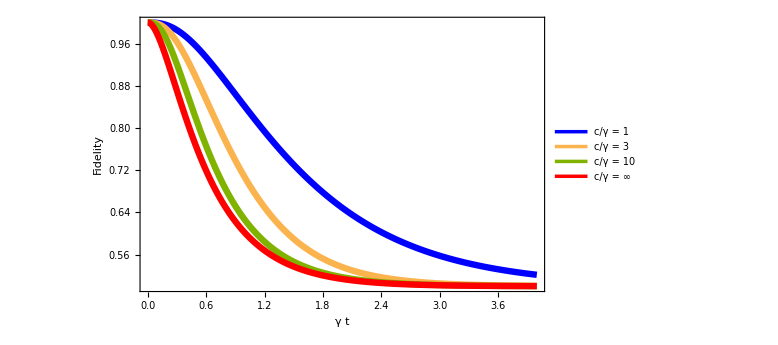

/Users/jgarcian/Documents/Paper2026/Images/fidkerc.pdf

```mathematica
(*Markov limit c->Infinity*)
FpmmeMarkov[t_?NumericQ,γ_?NumericQ,η_?NumericQ]:=Module[{Δ},Δ=Sqrt[16 γ^2+16 γ η+η^2];
1/2+(1/2)*Exp[-t (4 γ+η/2)]*(Cosh[(t/2) Δ]+((8 γ+η)*Sinh[(t/2) Δ]/Δ))];

(*convenience wrapper:allow c=Infinity*)
Fpmme2[t_?NumericQ,γ_?NumericQ,η_?NumericQ,c_]:=If[c===Infinity,FpmmeMarkov[t,γ,η],Fpmme[t,γ,η,c]];
(* =====================*)
(*Parameters for plot*)
(* =====================*)
γval=1.0;
ηval=0.0;                 
tMin=0.0;
tMax=4.0;
cOverGammaVals={1,3,10,Infinity};
cVals=cOverGammaVals/. Infinity->Infinity/. r_?NumericQ:>r*γval;
nPts=400;
tGrid=Subdivide[tMin,tMax,nPts];
(*numeric datasets:each is {{t,F(t)},...}*)
dataSets=Table[Transpose@{N@tGrid,N@Map[Fpmme2[#,γval,ηval,c]&,tGrid]},{c,cVals}];

(* =======================*)
(*Export long-format CSV*)
(* =======================*)

longData=Flatten[MapIndexed[Function[{dataset,idx},With[{r=cOverGammaVals[[idx[[1]]]]},({If[r===Infinity,"Infinity",N@r],#[[1]],#[[2]]}&/@dataset)]],dataSets],1];

Export["/Users/jgarcian/Documents/Paper2026/Datasets/fidkerc_PMME_ηOverGamma_sweep_long.csv",Prepend[longData,{"c_over_gamma","t","Fidelity"}],"CSV"];
(* ==============*)
(*Plot styling*)
(* ==============*)
styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],(*blue*)Directive[Thickness[0.008],RGBColor[0.98,0.70,0.3]],(*orange*)Directive[Thickness[0.008],RGBColor[0.50,0.70,0.0]],(*green*)Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]     (*red*)};
legendLabels={Row[{Style["c",18],"/",Style["γ",18]," = 1"}],Row[{Style["c",18],"/",Style["γ",18]," = 3"}],Row[{Style["c",18],"/",Style["γ",18]," = 10"}],Row[{Style["c",18],"/",Style["γ",18]," = ∞"}]};

fidkercPlot=ListLinePlot[dataSets,InterpolationOrder->3,PlotStyle->Take[styles,Length@dataSets],PlotRange->{{tMin,tMax},{0.5,1.0}},Axes->True,Frame->True,FrameStyle->Directive[Black,Thick,23],AxesOrigin->{tMin,0.5},TicksStyle->Directive[Black,14],PlotLegends->Placed[LineLegend[legendLabels,LegendMarkerSize->23,LabelStyle->Directive[Black,23]],Right],AspectRatio->0.6,FrameLabel->{{Style["Fidelity",25],None},{Style["γ t",25],None}},ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/fidkerc.pdf",fidkercPlot]
```

## Five qubit code

### Theory

{1/36 (-29-√217),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1/36 (-29+√217),0,0,0}

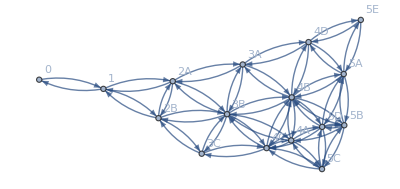

```mathematica
kLapExpKernel[s_,c_,λ_]:=c/((s-λ)+c)
L0five[η_]:=η{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-2/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/9,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,1/3,0,1/6,0,1/3,0,0,1/2,-1/9,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}

Total[L0five[η],{1}];
Eigenvalues[L0five[1]]
L1five[γ_]:=γ{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}};
Total[L1five[γ],{1}];
Eigenvalues[L1five[1]];

AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0},{0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,0},{0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0},{0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1},{0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}},DirectedEdges->True,VertexLabels->{1->"0",2->"1",3->"2A",4->"2B",5->"3A",6->"3B",7->"3C",8->"4A",9->"4B",10->"4C",11->"4D",12->"5A",13->"5B",14->"5C",15->"5D",16->"5E"}]
```

```mathematica
PmmeMat5ExpKernelwihtKis[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ,k1_,k2_,k3_,k4_,k5_,k6_,k7_,k8_,k9_,k10_,k11_,k12_,k13_,k14_,k15_,k16_]:=-s IdentityMatrix[16]+L0five[η]+(L1five[γ].Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]).(DiagonalMatrix[{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,k12,k13,k14,k15,k16}].Inverse[Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]])

kLapExpKernel[s_,c_,λ_]:=c/((s-λ)+c)

L1five[γ_]:=γ{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}};
MatrixForm[L1five[1]] (*for gamma=1*)
Total[L1five[γ],{1}] (*checking that they sum up to zero*)
Eigenvalues[L1five[1]] (*checking the eigenvals*)
NullSpace[L1five[1]](*checking that the stationary state is the max mixed state*)

(*Recover the matrix using the eigendecomposition*)
Transpose[Eigenvectors[L1five[γ]]].DiagonalMatrix[Eigenvalues[L1five[γ]]].Inverse[Transpose[Eigenvectors[L1five[γ]]]]==L1five[γ]
L0fivecorrect[η_]:=η{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-1/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/6,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,1/6,0,1/3,0,0,1/2,-1/6,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}
MatrixForm[L0fivecorrect[1]];(*for eta=1*)
Eigenvalues[L0fivecorrect[1]];(*checking the eigenvalues*)
NullSpace[L0fivecorrect[1]](*the stationary state are rho0 (corrected),rho5E (logical X^5,...),and linear comb 2rho3B+rho4A+rho5C*)

FullSimplify[Transpose[Eigenvectors[L0fivecorrect[η]]].DiagonalMatrix[Eigenvalues[L0fivecorrect[η]]].Inverse[Transpose[Eigenvectors[L0fivecorrect[η]]]]]==L0fivecorrect[η]

Laplace5Markov[s_,γ_?NumericQ,η_?NumericQ]:=-s IdentityMatrix[16]+L0fivecorrect[η]+L1five[γ]
overlap5Markov[t_,γ_,η_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[Laplace5Markov[s,γ,η]].{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[1]],s,t]+ResourceFunction["NInverseLaplaceTransform"][(Inverse[Laplace5Markov[s,γ,η]].{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[2]],s,t]
MatrixForm[L1five[γ]+L0fivecorrect[η]];
NullSpace[L1five[1]+L0fivecorrect[0]];
M5totalγη[γ_,η_]:=L1five[γ]+L0fivecorrect[η]
(*ListPlot[{Table[{t,overlap5Markov[t,1,0]},{t,0.1,3,0.2}],Table[{t,overlap5Markov[t,1,100]},{t,0.1,3,0.2}],Table[{t,overlap5Markov[t,1,300]},{t,0.1,3,0.2}],Table[{t,overlap5Markov[t,1,1000]},{t,0.1,3,0.2}]},PlotStyle->{Blue,Red,Yellow,Purple},PlotLegends->{"η/γ=0","η/γ=100","η/γ=300","η/γ=1000"},PlotMarkers->Automatic,Joined->True]*)
```

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-20,-20,-20,-20,-20,-16,-16,-16,-16,-12,-12,-12,-8,-8,-4,0}

{{1,15,30,60,30,180,60,90,120,180,15,30,60,90,60,3}}

True

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,2,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

True

```mathematica
truncateToSixDecimals[x_?NumericQ]:=Floor[x*10^6]/10^6;
truncateToSixDecimals[x_]:=x;  (*lets Map work on matrices safely*)
PmmeMat5ExpKernelAgain6FastStable[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=Module[{M,vals,vecs,Vt,kdiag},M=M5totalγη[γ,η];
{vals,vecs}=Eigensystem[N[M]];
vals=truncateToSixDecimals/@vals;
Vt=Transpose[truncateToSixDecimals/@vecs];
kdiag=DiagonalMatrix[kLapExpKernel[s,c,#]&/@vals];
-s IdentityMatrix[16]+L0fivecorrect[η]+(L1five[γ].Vt).kdiag.LinearSolve[Vt,IdentityMatrix[16]]]
PmmeMat5ExpKernelAgain6FastStable[s,1,1,1]//MatrixRank
PmmeMat5ExpKernelAgain6FastStable[1,1,1,1]//MatrixRank
overlap5PMMEwithapprox[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[PmmeMat5ExpKernelAgain6FastStable[s,γ,η,c]].{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[1]],s,t]+ResourceFunction["NInverseLaplaceTransform"][(Inverse[PmmeMat5ExpKernelAgain6FastStable[s,γ,η,c]].{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[2]],s,t]
```

11

16

### Plot Markov

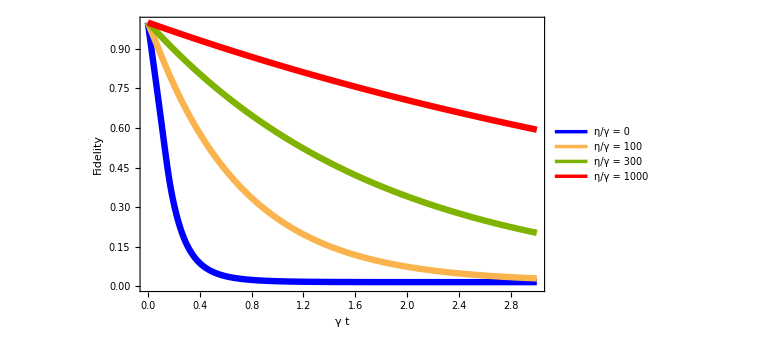

/Users/jgarcian/Documents/Paper2026/Images/fiveqmarkov.pdf

```mathematica
etas={0,100,300,1000};
γ=1;

tmin=0.1;tmax=3;
tGrid=Subdivide[tmin,tmax,40];   (*increase points modestly for smoothness*)
dataSets=
ParallelTable[With[{η=ηval},{#,overlap5Markov[#,γ,η]}&/@tGrid],{ηval,etas}];
longData=Flatten[MapIndexed[Function[{dataset,idx},With[{ratio=etas[[idx[[1]]]]},({ratio,#[[1]],#[[2]]}&/@dataset)]],dataSetsWithZero],1];

Export["Markov_fidelity_five_datasets.csv",Prepend[longData,{"/Users/jgarcian/Documents/Paper2026/Datasets/fiveqmarkov_eta_over_gamma","t","Fidelity"}],"CSV"];

(*ListLinePlot[dataSets,InterpolationOrder->3,(*cubic spline*)PlotMarkers->None]*)
legendLabels={Row[{Style["η",23],"/",Style["γ",23]," = 0"}],Row[{Style["η",23],"/",Style["γ",23]," = 100"}],Row[{Style["η",23],"/",Style["γ",23]," = 300"}],Row[{Style["η",23],"/",Style["γ",23]," = 1000 "}]};

dataSetsWithZero=Prepend[#,{0,1}]&/@dataSets;
fiveqmarkovPlot=ListLinePlot[dataSetsWithZero,InterpolationOrder->3,PlotMarkers->None,PlotStyle->Take[styles,Length@dataSetsWithZero],PlotRange->{{0,3},{0.0,1.0}},Frame->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,23],FrameLabel->{{Style["Fidelity",26],None},{Style["γ t",26],None}},BaseStyle->Directive[Black,23],PlotLegends->Placed[LineLegend[legendLabels,LegendMarkerSize->23],Right],AspectRatio->0.6,ImageSize->Large]

(*fiveqmarkov*)
(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/fiveqmarkov.pdf",fiveqmarkovPlot]
```

### Truncate data fo PMME

#### Theory

```mathematica
truncateToSixDecimals[number_]:=Floor[number*10^6]/10^6
M5totalγη[γ_,η_]:=L1five[γ]+L0fivecorrect[η];
PmmeMat5ExpKernelAgain6[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=-s IdentityMatrix[16]+L0fivecorrect[η]+(L1five[γ].Transpose[Map[truncateToSixDecimals,N[Eigenvectors[M5totalγη[γ,η]]]]]).(DiagonalMatrix[{kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[1]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[2]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[3]]]],
kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[4]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[5]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[6]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[7]]]],
kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[8]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[9]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[10]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[11]]]],
kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[12]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[13]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[14]]]],kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[15]]]],
kLapExpKernel[s,c,truncateToSixDecimals[Eigenvalues[M5totalγη[γ,η]][[16]]]]}].Inverse[Transpose[Map[truncateToSixDecimals,N[Eigenvectors[M5totalγη[γ,η]]]]]])

overlap5PMMEwithapprox[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[PmmeMat5ExpKernelAgain6[s,γ,η,c]].{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[1]],s,t]+ResourceFunction["NInverseLaplaceTransform"][(Inverse[PmmeMat5ExpKernelAgain6[s,γ,η,c]].{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[2]],s,t]
```

```mathematica
γval=1.0;          
tMin=0.1;
tMax=3.0;
ηVals={1,100,300,1000};
nPts=20;
tGrid=Subdivide[tMin,tMax,nPts];
dataSets=ParallelTable[Transpose@{N@tGrid,N@Map[overlap5PMMEwithapprox[#,1,η,1]&,tGrid]},{η,ηVals}];

(* =======================*)
(*Export long-format CSV*)
(* =======================*)
longData=Flatten[MapIndexed[Function[{dataset,idx},With[{r=N@ηVals[[idx[[1]]]]},({r,#[[1]],#[[2]]}&/@dataset)]],dataSets],1];

Export["PMME_etaOverGamma_sweep_long.csv",Prepend[longData,{"eta_over_gamma","t","Fidelity"}],"CSV"];
(* ==============*)
(*Plot styling*)
(* ==============*)
styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],(*blue*)Directive[Thickness[0.008],RGBColor[0.98,0.70,0.3]],(*orange*)Directive[Thickness[0.008],RGBColor[0.50,0.70,0.0]],(*green*)Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]     (*red*)};
legendLabels={Row[{Style["η",18],"/",Style["γ",18]," = 1"}],Row[{Style["η",18],"/",Style["γ",18]," = 100"}],Row[{Style["η",18],"/",Style["γ",18]," = 300"}],Row[{Style["η",18],"/",Style["γ",18]," = 1000"}]};
ListLinePlot[dataSets,InterpolationOrder->3,PlotStyle->Take[styles,Length@dataSets],PlotRange->{{tMin,tMax},{0.0,1.0}},Axes->True,Frame->True,FrameStyle->Directive[Black,Thick,18],AxesOrigin->{tMin,0.5},TicksStyle->Directive[Black,14],PlotLegends->Placed[LineLegend[legendLabels,LegendMarkerSize->18,LabelStyle->Directive[Black,18]],Right],AspectRatio->0.6,FrameLabel->{{Style["Fidelity",20],None},{Style["γ t",20],None}},ImageSize->Large]
```

```mathematica
dataSets=Import["PMME_etaOverGamma_sweep_long.csv"]
Length[dataSets]
```

{{eta_over_gamma,t,Fidelity},{1.,0.1,0.985482},{1.,0.245,0.90744},{1.,0.39,0.80618},{1.,0.535,0.706957},{1.,0.68,0.616864},{1.,0.825,0.537208},{1.,0.97,0.46754},{1.,1.115,0.406916},{1.,1.26,0.354296},{1.,1.405,0.308686},{1.,1.55,0.269185},{1.,1.695,0.234989},{1.,1.84,0.205396},{1.,1.985,0.17979},{1.,2.13,0.157636},{1.,2.275,0.13847},{1.,2.42,0.12189},{1.,2.565,0.107547},{1.,2.71,0.0951403},{1.,2.855,0.0844078},{1.,3.,0.0751237},{100.,0.1,0.994442},{100.,0.245,0.967405},{100.,0.39,0.924467},{100.,0.535,0.871414},{100.,0.68,0.812573},{100.,0.825,0.751136},{100.,0.97,0.689413},{100.,1.115,0.62904},{100.,1.26,0.571133},{100.,1.405,0.516416},{100.,1.55,0.465319},{100.,1.695,0.418054},{100.,1.84,0.374673},{100.,1.985,0.335115},{100.,2.13,0.299243},{100.,2.275,0.266867},{100.,2.42,0.237764},{100.,2.565,0.211696},{100.,2.71,0.18842},{100.,2.855,0.167694},{100.,3.,0.149284},{300.,0.1,0.997555},{300.,0.245,0.985875},{300.,0.39,0.966428},{300.,0.535,0.940986},{300.,0.68,0.911025},{300.,0.825,0.877769},{300.,0.97,0.842232},{300.,1.115,0.805244},{300.,1.26,0.767485},{300.,1.405,0.729505},{300.,1.55,0.691744},{300.,1.695,0.654553},{300.,1.84,0.618204},{300.,1.985,0.582907},{300.,2.13,0.548818},{300.,2.275,0.516049},{300.,2.42,0.484675},{300.,2.565,0.454742},{300.,2.71,0.426271},{300.,2.855,0.399264},{300.,3.,0.373709},{1000.,0.1,0.999175},{1000.,0.245,0.995265},{1000.,0.39,0.988607},{1000.,0.535,0.979656},{1000.,0.68,0.968803},{1000.,0.825,0.956384},{1000.,0.97,0.942687},{1000.,1.115,0.92796},{1000.,1.26,0.912415},{1000.,1.405,0.896233},{1000.,1.55,0.879571},{1000.,1.695,0.862561},{1000.,1.84,0.845316},{1000.,1.985,0.827932},{1000.,2.13,0.81049},{1000.,2.275,0.79306},{1000.,2.42,0.775699},{1000.,2.565,0.758456},{1000.,2.71,0.741372},{1000.,2.855,0.724481},{1000.,3.,0.70781}}

85

(eta_over_gamma | t | Fidelity
1. | 0.1 | 0.985482
1. | 0.245 | 0.90744
1. | 0.39 | 0.80618
1. | 0.535 | 0.706957
1. | 0.68 | 0.616864
1. | 0.825 | 0.537208
1. | 0.97 | 0.46754
1. | 1.115 | 0.406916
1. | 1.26 | 0.354296
1. | 1.405 | 0.308686
1. | 1.55 | 0.269185
1. | 1.695 | 0.234989
1. | 1.84 | 0.205396
1. | 1.985 | 0.17979
1. | 2.13 | 0.157636
1. | 2.275 | 0.13847
1. | 2.42 | 0.12189
1. | 2.565 | 0.107547
1. | 2.71 | 0.0951403
1. | 2.855 | 0.0844078
1. | 3. | 0.0751237
100. | 0.1 | 0.994442
100. | 0.245 | 0.967405
100. | 0.39 | 0.924467
100. | 0.535 | 0.871414
100. | 0.68 | 0.812573
100. | 0.825 | 0.751136
100. | 0.97 | 0.689413
100. | 1.115 | 0.62904
100. | 1.26 | 0.571133
100. | 1.405 | 0.516416
100. | 1.55 | 0.465319
100. | 1.695 | 0.418054
100. | 1.84 | 0.374673
100. | 1.985 | 0.335115
100. | 2.13 | 0.299243
100. | 2.275 | 0.266867
100. | 2.42 | 0.237764
100. | 2.565 | 0.211696
100. | 2.71 | 0.18842
100. | 2.855 | 0.167694
100. | 3. | 0.149284
300. | 0.1 | 0.997555
300. | 0.245 | 0.985875
300. | 0.39 | 0.966428
300. | 0.535 | 0.940986
300. | 0.68 | 0.911025
300. | 0.825 | 0.877769
300. | 0.97 | 0.842232
300. | 1.115 | 0.805244
300. | 1.26 | 0.767485
300. | 1.405 | 0.729505
300. | 1.55 | 0.691744
300. | 1.695 | 0.654553
300. | 1.84 | 0.618204
300. | 1.985 | 0.582907
300. | 2.13 | 0.548818
300. | 2.275 | 0.516049
300. | 2.42 | 0.484675
300. | 2.565 | 0.454742
300. | 2.71 | 0.426271
300. | 2.855 | 0.399264
300. | 3. | 0.373709
1000. | 0.1 | 0.999175
1000. | 0.245 | 0.995265
1000. | 0.39 | 0.988607
1000. | 0.535 | 0.979656
1000. | 0.68 | 0.968803
1000. | 0.825 | 0.956384
1000. | 0.97 | 0.942687
1000. | 1.115 | 0.92796
1000. | 1.26 | 0.912415
1000. | 1.405 | 0.896233
1000. | 1.55 | 0.879571
1000. | 1.695 | 0.862561
1000. | 1.84 | 0.845316
1000. | 1.985 | 0.827932
1000. | 2.13 | 0.81049
1000. | 2.275 | 0.79306
1000. | 2.42 | 0.775699
1000. | 2.565 | 0.758456
1000. | 2.71 | 0.741372
1000. | 2.855 | 0.724481
1000. | 3. | 0.70781)

#### Plot

```mathematica
longData=Import["PMME_etaOverGamma_sweep_long.csv"];
longData=longData[[1;;85]];
recoveredDataSets=Table[Select[longData,#[[1]]==eta&][[All,{2,3}]],{eta,etas}];
recoveredDataSetsfirst={{0.1,0.9854823112081953},{0.24500000000000002,0.9074395729717406},{0.39000000000000007,0.8061800879137188},{0.535,0.7069565439190635},{0.6800000000000002,0.6168644206495216},{0.825,0.5372076651124571},{0.9700000000000001,0.46754046427521817},{1.115,0.4069162049973022},{1.2600000000000002,0.3542958167615943},{1.405,0.30868613916364473},{1.55,0.26918461538214344},{1.695,0.23498936438102067},{1.8400000000000003,0.2053960379351326},{1.985,0.17978980065860561},{2.13,0.15763587189418768},{2.275,0.13847008968456298},{2.4200000000000004,0.12189010405391999},{2.5650000000000004,0.10754742122685094},{2.71,0.09514034235482252},{2.855,0.08440775938423689},{3.,0.07512373674432046}};
```

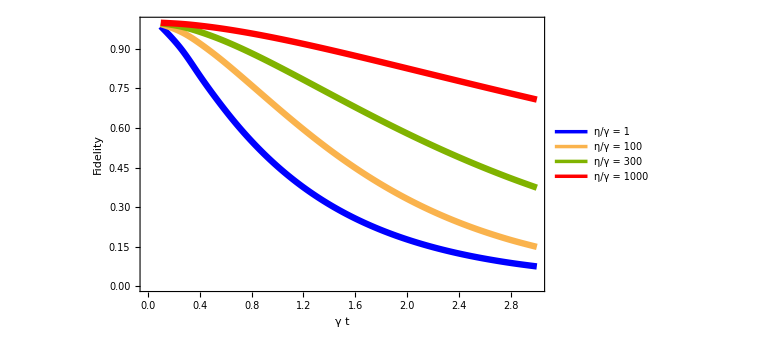

/Users/jgarcian/Documents/Paper2026/Images/PMMEfiveq.pdf

```mathematica
(* ==============*)
(*Plot styling*)
(* ==============*)
styles={Directive[Thickness[0.008],RGBColor[0.0,0.0,1.0]],(*blue*)Directive[Thickness[0.008],RGBColor[0.98,0.70,0.3]],(*orange*)Directive[Thickness[0.008],RGBColor[0.50,0.70,0.0]],(*green*)Directive[Thickness[0.008],RGBColor[1.0,0.0,0.0]]     (*red*)};
legendLabels={Row[{Style["η",23],"/",Style["γ",23]," = 1"}],Row[{Style["η",23],"/",Style["γ",23]," = 100"}],Row[{Style["η",23],"/",Style["γ",23]," = 300"}],Row[{Style["η",23],"/",Style["γ",23]," = 1000"}]};
PMMEfiveqplot=ListLinePlot[{recoveredDataSetsfirst,recoveredDataSets[[2]],recoveredDataSets[[3]],recoveredDataSets[[4]]},InterpolationOrder->3,PlotStyle->Take[styles,4],PlotRange->{{0,3},{0.0,1.0}},Axes->True,Frame->True,FrameStyle->Directive[Black,Thick,18],AxesOrigin->{tMin,0.5},TicksStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLegends->Placed[LineLegend[legendLabels,LegendMarkerSize->23,LabelStyle->Directive[Black,23]],Right],AspectRatio->0.6,FrameLabel->{{Style["Fidelity",20],None},{Style["γ t",25],None}},ImageSize->Large]

(*----------EXPORT AS PDF----------*)
Export["/Users/jgarcian/Documents/Paper2026/Images/PMMEfiveq.pdf",PMMEfiveqplot]
```